```mathematica
Clear["Global`*"]
(*Defififinition of f=f(x,t)*)
f1[x_,y_,t_]= y;
f2[x_,y_,t_]= -4 Pi x;
(*Error message*)
approximate::nonnegativeint="'N' must be replaced by a non-negative integer.";

(*Construction of successively approximate sequences t:time;x0:initial value;N:number of iterations The initial time t0 is always 0*)

approximate[t_,x0_,y0_,N_]:=Module[{k=0}, If[Or[N<0,Not[IntegerQ[N]]],Message[approximate::nonnegativeint,N],
x[0,s_]:=x0;
y[0,s_]:= y0;
While[k<N,
x[k_,s_]:=(x[k,s]=x0+Integrate[f1[x[k−1,u],y[k-1,u],u],{u,0,s}]);
y[k_,s_]:=(y[k,s]=y0+Integrate[f2[x[k-1,u],y[k-1,u],u],{u,0,s}]) ;
k++];(*Instead of “While,” you can also use “For” and “Do”*)
{x[N,t], y[N,t]}
]
];
(*An example of “approximate”*)
approximate[1,1,1,7]
```

{2-(8 π)/3+(4 π^2)/5-(32 π^3)/315,1-6 π+(10 π^2)/3-(28 π^3)/45+(16 π^4)/315}

{{1.,1.},{1.03574,-0.29266},{0.942686,-1.54893},{0.732404,-2.61258},{0.431046,-3.35135},{0.0760849,-3.67337},{-0.288337,-3.53859},{-0.616904,-2.96378},{-0.868756,-2.02041},{-1.01258,-0.8258},{-1.03048,0.471503},{-0.920238,1.71017},{-0.695563,2.73618},{-0.384392,3.42194},{-0.0254212,3.68218},{0.33671,3.48461},{0.65697,2.85399},{0.895534,1.86938},{1.02275,0.655178},{1.02288,-0.632035},{0.89615,-1.81712},{0.659183,-2.71405},{0.343956,-3.11666},{-0.00341726,-2.75261},{-0.321831,-1.16451},{-0.527662,2.548},{-0.49187,10.2457},{0.0145813,25.7424},{1.43707,56.6483},{4.67003,117.712},{11.5031,236.74},{25.4499,464.884},{53.2477,894.157},{107.51,1686.76},{211.327,3123.32},{406.082,5681.04},{764.521,10158.2},{1412.22,17870.3},{2562.35,30953.4},{4571.,52830.2},{8024.34,88913.5},{13873.7,147660.},{23642.7,242128.},{39740.9,392262.},{65933.9,628198.},{108040.,995026.},{174950.,1.55956×10^6},{280117.,2.41988×10^6},{443691.,3.71878×10^6},{695572.,5.6623×10^6},{1.07974×10^6,8.54549×10^6},{1.66031×10^6,1.27875×10^7},{2.53001×10^6,1.89795×10^7},{3.82189×10^6,2.79494×10^7},{5.72542×10^6,4.08487×10^7},{8.50843×10^6,5.92684×10^7},{1.25469×10^7,8.53934×10^7},{1.83653×10^7,1.22206×10^8},{2.669×10^7,1.73751×10^8},{3.85214×10^7,2.4549×10^8},{5.52288×10^7,3.44748×10^8},{7.86755×10^7,4.81308×10^8},{1.11383×10^8,6.68161×10^8},{1.56746×10^8,9.22482×10^8},{2.1931×10^8,1.26686×10^9},{3.05131×10^8,1.73089×10^9},{4.2224×10^8,2.35315×10^9},{5.81235×10^8,3.18372×10^9},{7.96043×10^8,4.28736×10^9},{1.08488×10^9,5.74748×10^9},{1.47146×10^9,7.67103×10^9},{1.98658×10^9,1.01947×10^10},{2.66998×10^9,1.34927×10^10},{3.57285×10^9,1.77857×10^10},{4.7608×10^9,2.3353×10^10},{6.31765×10^9,3.05466×10^10},{8.3501×10^9,3.98085×10^10},{1.09935×10^10,5.16922×10^10},{1.44191×10^10,6.68888×10^10},{1.88425×10^10,8.6258×10^10},{2.45347×10^10,1.10867×10^11},{3.18351×10^10,1.42037×10^11},{4.11674×10^10,1.81397×10^11},{5.30594×10^10,2.30953×10^11},{6.81661×10^10,2.93167×10^11},{8.72984×10^10,3.71053×10^11},{1.11458×10^11,4.68294×10^11},{1.41877×10^11,5.89375×10^11},{1.80072×10^11,7.3975×10^11},{2.27898×10^11,9.26029×10^11},{2.87623×10^11,1.15622×10^12},{3.62013×10^11,1.43997×10^12},{4.54435×10^11,1.78892×10^12},{5.68972×10^11,2.21707×10^12},{7.1057×10^11,2.7412×10^12},{8.85208×10^11,3.38139×10^12},{1.10009×10^12,4.16167×10^12},{1.3639×10^12,5.11067×10^12},{1.68705×10^12,6.26249×10^12},{2.08202×10^12,7.65763×10^12},{2.56375×10^12,9.34413×10^12}}

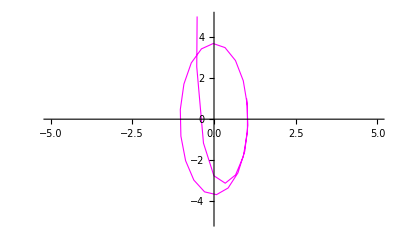

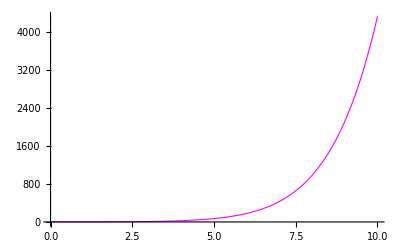

```mathematica
(*Numerical solution (data):k=number of iterations;d=[step size];tlast=[last time]*)nsol[k_,d_,x0_,y0_,tlast_]:=Table[approximate[t,x0,y0,k],{t,0,tlast,d}];
ngraph[k_,d_,x0_,y0_,tlast_]:=ListLinePlot[nsol[k,d,x0,y0,tlast],PlotStyle->{Thickness[0.002],RGBColor[1,0,1]},PlotRange->{{-5,5},{-5,5}}];
(*Graph of the numerical solution:k=3;d=0:1;x0=1;tlast=10*)
nsol[20,0.1,1,1,10]
ngraph[20,0.1,1,1,10]
```

```mathematica
(*Analytical solution:x0=1*)
asol[x0_,y0_]:=DSolve[{x '[t]==f1[x[t],y[t],t],y'[t]==f2[x[t],y[t],t],x[0]==x0,y[0]==y0},{x[t],y[t]},t];
asol[1,1]
```

{{x[t]→(2 √π Cos[2 √π t]+Sin[2 √π t])/(2 √π),y[t]→Cos[2 √π t]-2 √π Sin[2 √π t]}}

```mathematica
{{x[t]->(2 √π Cos[2 √π t]+Sin[2 √π t])/(2 √π),y[t]->Cos[2 √π t]-2 √π Sin[2 √π t]}}
```

{{x[t]→(2 √π Cos[2 √π t]+Sin[2 √π t])/(2 √π),y[t]→Cos[2 √π t]-2 √π Sin[2 √π t]}}

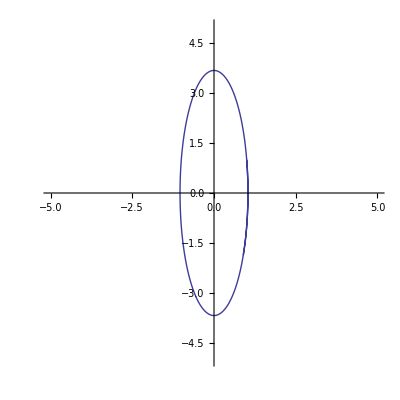

```mathematica
(*Graph of the analytical solution:x0=1;tlast=10*) agraph[x0_,y0_,tlast_]:=ParametricPlot[Evaluate[{x[t],y[t]}/.asol[x0,y0]],{t,0,tlast},PlotRange->{{-5,5},{-5,5}}]
agraph[1,1,2]
```

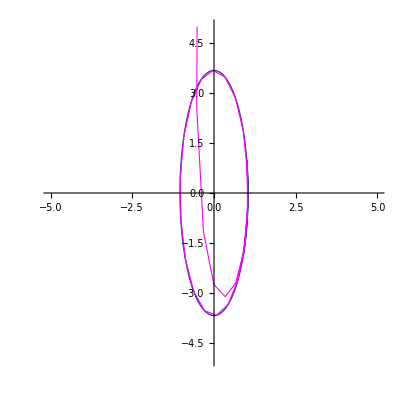

```mathematica
Show[agraph[1,1,2],ngraph[20,0.1,1,1,3]]
```

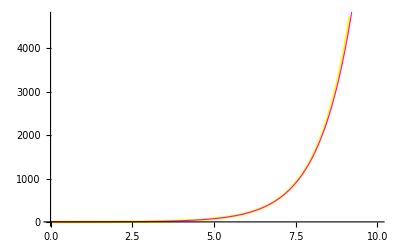

```mathematica
Show[agraph[1,10],ngraph[14,0.1,1,10]]
```

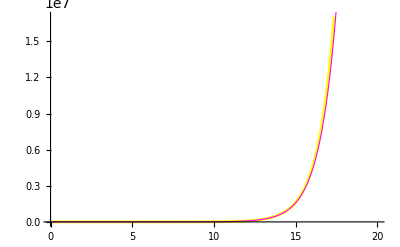

```mathematica
Show[agraph[1,20],ngraph[22,0.1,1,20]]
```

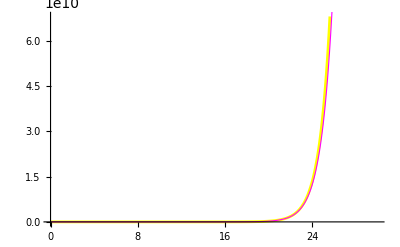

```mathematica
Show[agraph[1,30],ngraph[30,0.1,1,30]]
```